```mathematica
Quiet[Remove["Global`*"],{Remove::rmnsm}];Print["Mathematica $Version = “",$Version,"”"];Print["Execution time = ",DateString[DateList[],{"Hour",":","Minute"," on ","DayNameShort"," ","Day"," ","MonthNameShort"," ","Year"}]];
```

Mathematica $Version = “9.0 for Mac OS X x86 (64-bit) (January 24, 2013)”

Execution time = 14:27 on Sun 10 Mar 2024

```mathematica
simplifyExtra:=Simplify[PowerExpand[Simplify[#]]]&;
```

```mathematica
KnotsFromCoeffsCubic[{c0_:0,c1_:0,c2_:0,c3_:0}]={c0,c0+c1/3,c0+(2c1+c2)/3,c0+c1+c2+c3};
CoeffsFromKnotsCubic[{z0_,z1_,z2_,z3_}]=PadRight[{z0,-3 z0+3 z1,3 z0-6 z1+3 z2,-z0+3 z1-3 z2+z3},4];
CoeffsBezierSplitCubic[coeffs_List,t0_,t1_]:=Module[{t},(PadRight[CoefficientList[Table[(t0*(1-t)+t1*t)^i,{i,0,3}].PadRight[coeffs,4,0],t],4,0])//simplifyExtra];
KnotsBezierSplitCubic[{z0_,z1_,z2_,z3_},t0_,t1_]:=KnotsFromCoeffsCubic[CoeffsBezierSplitCubic[CoeffsFromKnotsCubic[{z0,z1,z2,z3}],t0,t1]]//simplifyExtra;
```

```mathematica
(* Tests *)
Module[{knots={z0,z1,z2,z3}}, Print[knots==KnotsFromCoeffsCubic[CoeffsFromKnotsCubic[knots]]//Simplify]];
Module[{coeffs={c0,c1,c2,c3}}, Print[coeffs==CoeffsFromKnotsCubic[KnotsFromCoeffsCubic[coeffs]]//Simplify]];
```

True

True

```mathematica
xSize=40;  ySize=xSize*4/5;  distAway=ySize/8;
xOuter=xSize Cos[t π/2];
yOuter=ySize Sin[t π/2];
```

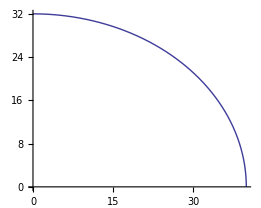

```mathematica
ParametricPlot[{xOuter,yOuter},{t,0,1}]
```

```mathematica
dx=D[xOuter,t];
dy=D[yOuter,t];
```

```mathematica
Print["xAway = ",xAway=FullSimplify[xOuter-distAway dy/Sqrt[dx^2+dy^2]]];
Print["yAway = ",yAway=FullSimplify[yOuter+distAway dx/Sqrt[dx^2+dy^2]]];
```

xAway = 8 Cos[(π t)/2] (5-(2 √2)/(√(41-9 Cos[π t])))

yAway = 4 (8-(5 √2)/(√(41-9 Cos[π t]))) Sin[(π t)/2]

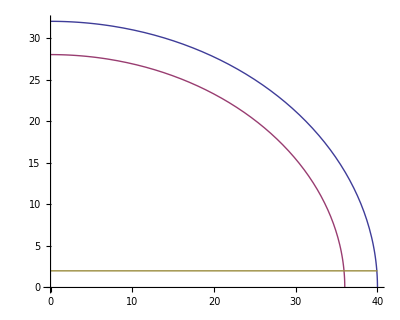

```mathematica
ParametricPlot[{
	{xOuter,yOuter},
	{xAway,yAway},
	{t*xSize,distAway/2}
},{t,0,1}]
```

```mathematica
tt=(t/.NSolve[yAway==(distAway/2)&&t≥0&&t≤1,t,WorkingPrecision->64]//FullSimplify)⟦1⟧
```

0.04718678092581780766594424477530721681092044307542972626190234735

```mathematica
(* Cubic with correct endpoints, and correct tangents at endpoints *)
x0=FullSimplify[xAway/.{t->tt}];
y0=distAway/2;
x1=x0+speed1*FullSimplify[D[xAway,t]/.{t->tt}];
y1=y0+speed1*FullSimplify[D[yAway,t]/.{t->tt}];
x2=x3-speed2*FullSimplify[D[xAway,t]/.{t->1}];
y2=ySize-distAway;
x3=0;
y3=ySize-distAway;
```

```mathematica
FullSimplify[{x0,y0,x3,y3}/.{t->tt}]
```

{35.9072933200111847479073612889266169790622393446371254606881381423,2,0,28}

```mathematica
knotsCubic=({{x0, x1, x2, x3}, {y0, y1, y2, y3}});
```

```mathematica
xCubic=Simplify[{1,t,t^2,t^3}.CoeffsFromKnotsCubic[knotsCubic⟦1⟧]];
yCubic=Simplify[{1,t,t^2,t^3}.CoeffsFromKnotsCubic[knotsCubic⟦2⟧]];
```

```mathematica
(* Solves for middle-ish being correct *) 
eqnMiddleish=Simplify[1==1/xSize^2(xCubic+(distAway D[yCubic,t])/Sqrt[D[xCubic,t]^2+D[yCubic,t]^2])^2+1/ySize^2(yCubic-(distAway D[xCubic,t])/Sqrt[D[xCubic,t]^2+D[yCubic,t]^2])^2];
eqnMiddleish1=Simplify[Chop[Simplify[eqnMiddleish/.{t->1/3}]]];
eqnMiddleish2=Simplify[Chop[Simplify[eqnMiddleish/.{t->2/3}]]];
speedsMiddleish=FindRoot[{eqnMiddleish1,eqnMiddleish2},{{speed1,0.34},{speed2,0.33}},WorkingPrecision->48]
```

FindRoot::precw: The precision of the argument function ({(26.59799505186013685030174910290860516967573284787935219310232 - « 117 »\ « 6 » + « 1 » + « 61 »\ Power[« 2 »])^2/1600 + (-« 115 » - 18.813845891084\ speed1 + Plus[« 2 »]\ Power[« 2 »])^2/1024 == 1, (-« 117 » - « 59 »\ speed1 + Plus[« 2 »]\ Power[« 2 »])^2/1024 + (« 117 » - « 116 »\ speed1 + Plus[« 2 »]\ Power[« 2 »] + « 117 »\ speed2)^2/1600 == 1}) is less than WorkingPrecision (48.).

{speed1→0.343769087671397307836674242061959637310285353884,speed2→0.326638558301373304364357876941065436563472449499}

```mathematica
N[knotsCubic/.speedsMiddleish,24]//MatrixForm
```

(35.9072933200111847479074 | 34.5565478898035591850252 | 18.8814414305531057247207 | 0
2. | 16.5521419345287670211269 | 28. | 28.)

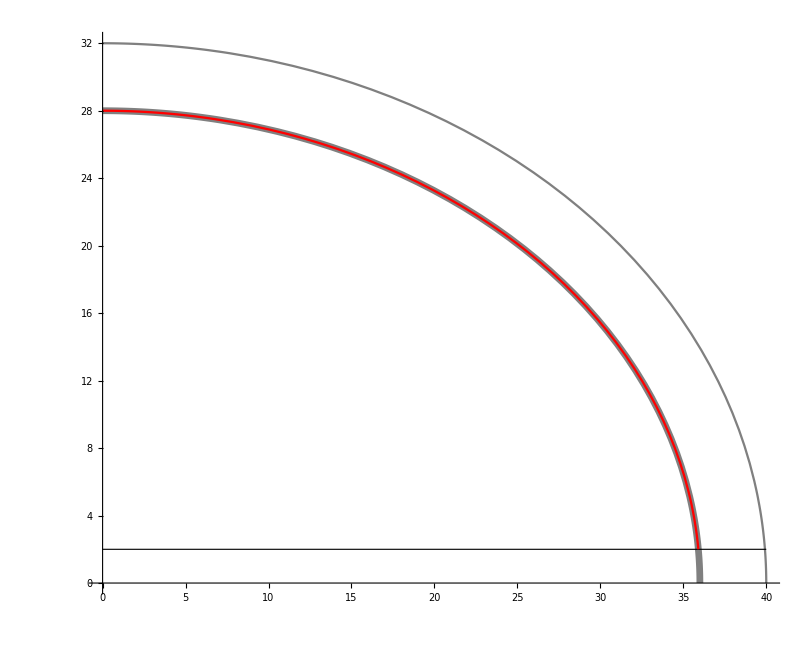

```mathematica
ParametricPlot[{
	{xOuter,yOuter},
	{xAway,yAway},
	{t*xSize,distAway/2},
	({xCubic,yCubic}/.speedsMiddleish)
},{t,0,1},PlotStyle->{{Gray,Thickness[0.002]},{Gray,Thickness[0.006]},{Black,Thickness[0.001]},{Red,Thickness[0.002]}}]
```

```mathematica
(* To be used in the SVG *)
(knotsUsed=Round[knotsCubic/.speedsMiddleish,0.0001])//MatrixForm
```

(35.9073 | 34.5565 | 18.8814 | 0.
2. | 16.5521 | 28. | 28.)

```mathematica
xAwayUsed=CoeffsFromKnotsCubic[knotsUsed⟦1⟧].{1,t,t^2,t^3};
yAwayUsed=CoeffsFromKnotsCubic[knotsUsed⟦2⟧].{1,t,t^2,t^3};
```

```mathematica
(* Make path distAway from used inner path. Scale by ellipse ratio such that radius should be 1. Compute said radius. *)
rPseudoAwayUsed=Simplify[√(1/xSize^2(xAwayUsed+(distAway D[yAwayUsed,t])/Sqrt[D[xAwayUsed,t]^2+D[yAwayUsed,t]^2])^2+1/ySize^2(yAwayUsed-(distAway D[xAwayUsed,t])/Sqrt[D[xAwayUsed,t]^2+D[yAwayUsed,t]^2])^2)];
```

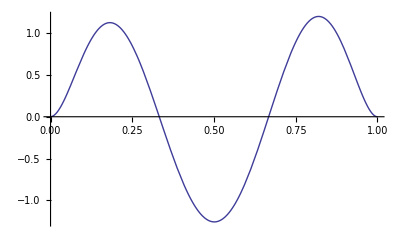

```mathematica
Plot[10000*(rPseudoAwayUsed-1),{t,0,1}]
```

```mathematica
(* Average error of pseudo-radius of implied external curve, in RMS sense *)
10000*Sqrt[NIntegrate[(rPseudoAwayUsed-1)^2,{t,0,1}]/(1-0)]
```

0.819099

```mathematica
(* Worst errors *)
tTurn=Map[t/.FindRoot[0==D[rPseudoAwayUsed,t],{t,#}]⟦1⟧&,{0.18,0.5,0.82}];
Prepend[Map[{t,10000(rPseudoAwayUsed-1),1/(rPseudoAwayUsed-1)}/.{t->#}&,tTurn],{"t","bp","1-in-"}]//MatrixForm
```

(t | bp | 1-in-
0.181609 | 1.12381 | 8898.26
0.500972 | -1.25589 | -7962.48
0.819999 | 1.19778 | 8348.8)